# Structure Factor Analysis

## Basic Settings

```mathematica
Quit[]
```

```mathematica
(* operators *)
LD=-d ksq;
KDsq=2 d nb ksq;
LR=-r;
KRsq=2G;
(* exact *)
Mexact=Exp[(LD+LR)dt];
Nsqexact=-(KDsq+KRsq)(1-Exp[2(LD+LR)dt])/2/(LD+LR);
Simplify[Nsqexact/(1-Mexact^2)];
Skexact=Evaluate[%];
Simplify[(((Skexact/.ksq->k^2)/.{k->Sqrt[r/d]xi})/.G->C nb r)/nb,Assumptions->d>0&&r>0];
Sk0[xi_]:=Evaluate[%];
(* some expressions *)
R[n_,tau_,Y_]:=(Exp[LR tau]-1)n+Sqrt[-KRsq(1-Exp[2LR tau])/2/LR]Y
R1[n_,tau_,Y_]:=LR tau n+Sqrt[KRsq tau]Y
Mmn[tau_]:=1+LD tau 
Nmnsq[tau_]:=(1-Mmn[tau]^2)nb
Dmn[n_,tau_,Y_]:=(Mmn[tau]-1)n+Sqrt[Nmnsq[tau]]Y
ksqexpr=Sin[k dx/2]^2/(dx/2)^2;
```

## Forward Euler Schemes

```mathematica
(* FwdEulerTau *)
Solve[ntmp==n0+LD n0 dt+Sqrt[KDsq dt]Y1+R1[n0,dt,Y2],ntmp];
n1=ntmp/.First[%];
(***)
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2;
Series[M-Mexact,{dt,0,2}]
Series[Nsq-Nsqexact,{dt,0,2}]
Sk=Nsq/(1-M^2);
Series[Sk-Skexact,{dt,0,1}]
Simplify[%/.{r->0,G->0}]
Simplify[((((Sk/.ksq->ksqexpr)/.{dt->a/r,dx->Sqrt[d a/r/b]})/.{k->Sqrt[r/d]xi})/.G->C nb r)/nb,Assumptions->d>0&&r>0];
SkFwdEulerTau[xi_]:=Evaluate[%]
```

(-1/2 d^2 ksq^2-d ksq r-r^2/2) dt^2+O[dt]^3

2 (G+d ksq nb) (d ksq+r) dt^2+O[dt]^3

1/2 (G+d ksq nb) dt+O[dt]^2

1/2 d ksq nb dt+O[dt]^2

```mathematica
(* FwdEulerSSA *)
Solve[ntmp==n0+LD n0 dt+Sqrt[KDsq dt]Y1+R[n0,dt,Y2],ntmp];
n1=ntmp/.First[%];
(***)
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2;
Series[M-Mexact,{dt,0,2}]
Series[Nsq-Nsqexact,{dt,0,2}]
Sk=Nsq/(1-M^2);
Series[Sk-Skexact,{dt,0,1}]
Simplify[%/.{r->0,G->0}]
Simplify[((((Sk/.ksq->ksqexpr)/.{dt->a/r,dx->Sqrt[d a/r/b]})/.{k->Sqrt[r/d]xi})/.G->C nb r)/nb,Assumptions->d>0&&r>0];
SkFwdEulerSSA[xi_]:=Evaluate[%]
```

(-1/2 d^2 ksq^2-d ksq r) dt^2+O[dt]^3

2 (d G ksq+d^2 ksq^2 nb+d ksq nb r) dt^2+O[dt]^3

((d^2 G ksq^2+d^3 ksq^3 nb+2 d^2 ksq^2 nb r+2 d ksq nb r^2) dt)/(2 (d ksq+r)^2)+O[dt]^2

1/2 d ksq nb dt+O[dt]^2

## Explicit Schemes

```mathematica
(* ExMidTau *)
Solve[ntmp==n0+LD n0 dt/2+Sqrt[KDsq dt/2] Y1+R1[n0,dt/2,Y2],ntmp];
ni=ntmp/.First[%];
Solve[ntmp==n0+LD ni dt+Sqrt[KDsq dt/2]Y1+Sqrt[KDsq dt/2]Y3+R1[n0,dt/2,Y2]+R1[2ni-n0,dt/2,Y4],ntmp];
n1=ntmp/.First[%];
(***)
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2+Coefficient[n1,Y4]^2;
Series[M-Mexact,{dt,0,3}]
Series[Nsq-Nsqexact,{dt,0,3}]
Sk=Nsq/(1-M^2);
Series[Sk-Skexact,{dt,0,3}]
Simplify[%/.{r->0,G->0}]
Simplify[((((Sk/.ksq->ksqexpr)/.{dt->a/r,dx->Sqrt[d a/r/b]})/.{k->Sqrt[r/d]xi})/.G->C nb r)/nb,Assumptions->d>0&&r>0];
SkExMidTau[xi_]:=Evaluate[%]
```

1/6 (d ksq+r)^3 dt^3+O[dt]^4

1/3 (-d^2 G ksq^2-d^3 ksq^3 nb-2 d G ksq r-2 d^2 ksq^2 nb r-G r^2-d ksq nb r^2) dt^3+O[dt]^4

1/8 (d^2 G ksq^2+d^3 ksq^3 nb+2 d G ksq r+2 d^2 ksq^2 nb r+G r^2+d ksq nb r^2) dt^3+O[dt]^(7/2)

1/8 d^3 ksq^3 nb dt^3+O[dt]^(7/2)

```mathematica
(* ExMidSSA *)
Solve[ntmp==n0+LD n0 dt/2+Sqrt[KDsq dt/2] Y1,ntmp];
nii=ntmp/.First[%];
Solve[ntmp==n0+LD n0 dt/2+Sqrt[KDsq dt/2] Y1+R[nii,dt/2,Y2],ntmp];
ni=ntmp/.First[%];
Solve[ntmp==n0+LD ni dt+Sqrt[KDsq dt/2]Y1+Sqrt[KDsq dt/2]Y3+R[nii,dt/2,Y2]+R[ni,dt/2,Y4],ntmp];
n1=ntmp/.First[%];
(***)
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2+Coefficient[n1,Y4]^2;
Series[M-Mexact,{dt,0,3}]
Series[Nsq-Nsqexact,{dt,0,3}]
Sk=Nsq/(1-M^2);
Series[Sk-Skexact,{dt,0,2}]
Simplify[Series[Sk-Skexact,{dt,0,3}]/.{r->0,G->0}]
Simplify[((((Sk/.ksq->ksqexpr)/.{dt->a/r,dx->Sqrt[d a/r/b]})/.{k->Sqrt[r/d]xi})/.G->C nb r)/nb,Assumptions->d>0&&r>0];
SkExMidSSA[xi_]:=Evaluate[%]
```

1/24 (4 d^3 ksq^3+6 d^2 ksq^2 r+3 d ksq r^2) dt^3+O[dt]^4

1/3 (-d^2 G ksq^2-d^3 ksq^3 nb-2 d G ksq r+d^2 ksq^2 nb r+2 d ksq nb r^2) dt^3+O[dt]^4

((-6 d^2 G ksq^2 r+6 d^3 ksq^3 nb r-5 d G ksq r^2+15 d^2 ksq^2 nb r^2+8 d ksq nb r^3) dt^2)/(24 (d ksq+r)^2)+O[dt]^(5/2)

1/8 d^3 ksq^3 nb dt^3+O[dt]^(7/2)

```mathematica
(* MN2Tau2ndMN2 *)
nMN=n0+Dmn[n0,dt/2,Y1];
ni=(1+LR dt/2)nMN+Sqrt[KRsq dt/2]Y2;
nTau=nMN+LR dt ni+Sqrt[KRsq dt/2] Y2+Sqrt[KRsq dt/2] Y3;
n1=nTau+Dmn[nTau,dt/2,Y4];
(***)
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2+Coefficient[n1,Y4]^2;
Series[M-Mexact,{dt,0,2}]
Series[Nsq-Nsqexact,{dt,0,2}]
Sk=Nsq/(1-M^2);
Series[Sk-Skexact,{dt,0,1}]
Limit[Limit[Sk-Skexact,G->0],r->0]
Simplify[((((Sk/.ksq->ksqexpr)/.{dt->a/r,dx->Sqrt[d a/r/b]})/.{k->Sqrt[r/d]xi})/.G->C nb r)/nb,Assumptions->d>0&&r>0];
SkMN2Tau2ndMN2[xi_]:=Evaluate[%]
```

-1/4 (d^2 ksq^2) dt^2+O[dt]^3

1/2 d^2 ksq^2 nb dt^2+O[dt]^3

((-d^2 G ksq^2+d^2 ksq^2 nb r) dt)/(4 (d ksq+r)^2)+O[dt]^(3/2)

0

```mathematica
(* MN2SSAMN2 *)
nMN=n0+Dmn[n0,dt/2,Y1];
nSSA=nMN+R[nMN,dt,Y2];
n1=nSSA+Dmn[nSSA,dt/2,Y3];
(***)
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2;
Series[M-Mexact,{dt,0,2}]
Series[Nsq-Nsqexact,{dt,0,2}]
Sk=Nsq/(1-M^2);
Series[Sk-Skexact,{dt,0,1}]
Limit[Limit[Sk-Skexact,G->0],r->0]
Simplify[((((Sk/.ksq->ksqexpr)/.{dt->a/r,dx->Sqrt[d a/r/b]})/.{k->Sqrt[r/d]xi})/.G->C nb r)/nb,Assumptions->d>0&&r>0];
SkMN2SSAMN2[xi_]:=Evaluate[%]
```

-1/4 (d^2 ksq^2) dt^2+O[dt]^3

1/2 d^2 ksq^2 nb dt^2+O[dt]^3

((-d^2 G ksq^2+d^2 ksq^2 nb r) dt)/(4 (d ksq+r)^2)+O[dt]^(3/2)

0

## Implicit Schemes

```mathematica
(* CN2Tau2ndCN2 *)
Solve[ntmp==n0+LD(n0/2+ntmp/2)dt/2+Sqrt[KDsq dt/2]Y1,ntmp];
nCN=ntmp/.First[%];
ni=(1+LR dt/2)nCN+Sqrt[KRsq dt/2]Y2;
nTau=nCN+LR dt ni+Sqrt[KRsq dt/2] Y2+Sqrt[KRsq dt/2] Y3;
Solve[ntmp==nTau+LD(nTau/2+ntmp/2)dt/2+Sqrt[KDsq dt/2]Y4,ntmp];
n1=ntmp/.First[%];
(***)
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2+Coefficient[n1,Y4]^2;
Series[M-Mexact,{dt,0,3}]
Series[Nsq-Nsqexact,{dt,0,3}]
Sk=Nsq/(1-M^2);
Series[Sk-Skexact,{dt,0,3}]
Limit[Limit[Sk-Skexact,G->0],r->0]
Simplify[((((Sk/.ksq->ksqexpr)/.{dt->a/r,dx->Sqrt[d a/r/b]})/.{k->Sqrt[r/d]xi})/.G->C nb r)/nb,Assumptions->d>0&&r>0];
SkCN2Tau2ndCN2[xi_]:=Evaluate[%]
```

(-1/48 d^3 ksq^3+r^3/6) dt^3+O[dt]^4

1/24 (-8 d^2 G ksq^2+d^3 ksq^3 nb-16 d G ksq r+8 d^2 ksq^2 nb r-8 G r^2+16 d ksq nb r^2) dt^3+O[dt]^4

((-3 d^3 G ksq^3-8 d^2 G ksq^2 r+3 d^3 ksq^3 nb r-8 d G ksq r^2+8 d^2 ksq^2 nb r^2+8 d ksq nb r^3) dt^2)/(16 (d ksq+r)^2)+((G r^4+d ksq nb r^4) dt^3)/(8 (d ksq+r)^2)+O[dt]^(7/2)

0

```mathematica
(* CN2SSACN2 *)
Solve[ntmp==n0+LD(n0/2+ntmp/2)dt/2+Sqrt[KDsq dt/2]Y1,ntmp];
nCN=ntmp/.First[%];
nSSA=nCN+R[nCN,dt,Y2];
Solve[ntmp==nSSA+LD(nSSA/2+ntmp/2)dt/2+Sqrt[KDsq dt/2]Y3,ntmp];
n1=ntmp/.First[%];
(***)
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2+Coefficient[n1,Y4]^2;
Series[M-Mexact,{dt,0,3}]
Series[Nsq-Nsqexact,{dt,0,3}]
Sk=Nsq/(1-M^2);
Series[Sk-Skexact,{dt,0,3}]
Limit[Limit[Sk-Skexact,G->0],r->0]
Simplify[((((Sk/.ksq->ksqexpr)/.{dt->a/r,dx->Sqrt[d a/r/b]})/.{k->Sqrt[r/d]xi})/.G->C nb r)/nb,Assumptions->d>0&&r>0];
SkCN2SSACN2[xi_]:=Evaluate[%]
```

-1/48 (d^3 ksq^3) dt^3+O[dt]^4

1/24 (-8 d^2 G ksq^2+d^3 ksq^3 nb-16 d G ksq r+8 d^2 ksq^2 nb r+16 d ksq nb r^2) dt^3+O[dt]^4

((-9 d^3 G ksq^3-24 d^2 G ksq^2 r+9 d^3 ksq^3 nb r-16 d G ksq r^2+24 d^2 ksq^2 nb r^2+16 d ksq nb r^3) dt^2)/(48 (d ksq+r)^2)+O[dt]^(7/2)

0

```mathematica
(* ImMidTau *)
Solve[ntmp==n0+LD ntmp dt/2+Sqrt[KDsq dt/2] Y1+R1[n0,dt/2,Y2],ntmp];
ni=ntmp/.First[%];
Solve[ntmp==n0+LD(n0/2+ntmp/2)dt+Sqrt[KDsq dt/2]Y1+Sqrt[KDsq dt/2]Y3+R1[n0,dt/2,Y2]+R1[2ni-n0,dt/2,Y4],ntmp];
n1=ntmp/.First[%];
(***)
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2+Coefficient[n1,Y4]^2;
Series[M-Mexact,{dt,0,3}]
Series[Nsq-Nsqexact,{dt,0,3}]
Sk=Nsq/(1-M^2);
Series[Sk-Skexact,{dt,0,3}]
Limit[Limit[Sk-Skexact,G->0],r->0]
Simplify[((((Sk/.ksq->ksqexpr)/.{dt->a/r,dx->Sqrt[d a/r/b]})/.{k->Sqrt[r/d]xi})/.G->C nb r)/nb,Assumptions->d>0&&r>0];
SkImMidTau[xi_]:=Evaluate[%]
```

1/12 (-d^3 ksq^3-3 d^2 ksq^2 r+2 r^3) dt^3+O[dt]^4

1/6 (d^2 G ksq^2+d^3 ksq^3 nb+2 d G ksq r+2 d^2 ksq^2 nb r-2 G r^2-2 d ksq nb r^2) dt^3+O[dt]^4

((-d G ksq r^2-d^2 ksq^2 nb r^2+G r^3+d ksq nb r^3) dt^3)/(8 (d ksq+r))+O[dt]^(7/2)

0

```mathematica
(* ImMidSSA *)
Solve[ntmp==n0+LD ntmp dt/2+Sqrt[KDsq dt/2] Y1,ntmp];
ni=ntmp/.First[%];
Solve[ntmp==n0+LD(n0/2+ntmp/2)dt+Sqrt[KDsq dt/2]Y1+Sqrt[KDsq dt/2]Y2+R[ni,dt,Y3],ntmp];
n1=ntmp/.First[%];
(***)
M=Coefficient[n1,n0];
Nsq=Coefficient[n1,Y1]^2+Coefficient[n1,Y2]^2+Coefficient[n1,Y3]^2;
Series[M-Mexact,{dt,0,3}]
Series[Nsq-Nsqexact,{dt,0,3}]
Sk=Nsq/(1-M^2);
Series[Sk-Skexact,{dt,0,3}]
Limit[Limit[Sk-Skexact,G->0],r->0]
Simplify[((((Sk/.ksq->ksqexpr)/.{dt->a/r,dx->Sqrt[d a/r/b]})/.{k->Sqrt[r/d]xi})/.G->C nb r)/nb,Assumptions->d>0&&r>0];
SkImMidSSA[xi_]:=Evaluate[%]
```

(-1/12 d^3 ksq^3-1/4 d^2 ksq^2 r) dt^3+O[dt]^4

1/6 (d^2 G ksq^2+d^3 ksq^3 nb-4 d G ksq r+2 d^2 ksq^2 nb r+4 d ksq nb r^2) dt^3+O[dt]^4

((-3 d^2 G ksq^2 r-2 d G ksq r^2+3 d^2 ksq^2 nb r^2+2 d ksq nb r^3) dt^2)/(6 (d ksq+r)^2)+((2 d^3 G ksq^3 r+d^2 G ksq^2 r^2-3 d^3 ksq^3 nb r^2-2 d^2 ksq^2 nb r^3) dt^3)/(8 (d ksq+r)^2)+O[dt]^(7/2)

0

## Plot S(k)

```mathematica
(* Schlogl parameters *)
k10=1.5;k20=0.6;k30=2.05;k40=2.95;nbVal=1.;
r0=-D[k10 n^2-k20 n^3+k30-k40 n,n]/.n->nbVal;
G0=(k10 n^2+k20 n^3+k30+k40 n)/2/.n->nbVal;
CVal=G0/nbVal/r0
```

2.02857

```mathematica
(* Simulation parameters *)
dxVal=1.;dtVal=1.;alphaVal=0.05;betaVal=0.25;
rm=alphaVal/r0
DFick=betaVal
```

0.0285714

0.25

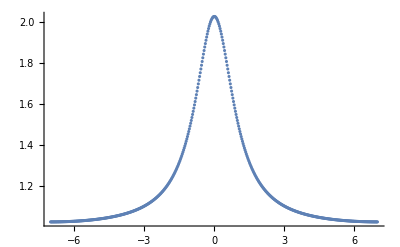

```mathematica
(* generate result *)
Ncell=512;
res=Table[{i Sqrt[betaVal/alphaVal]Pi/(Ncell/2),SkMN2SSAMN2[i Sqrt[betaVal/alphaVal]Pi/(Ncell/2)]/.{a->alphaVal,b->betaVal,C->CVal}},{i,-Ncell/2,Ncell/2-1}];
ListPlot[res]
```

```mathematica
(* save result *)
Export["res.dat",N[res],"Table"]
```

res.dat

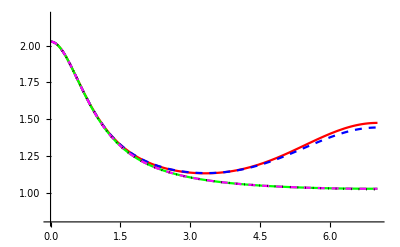

```mathematica
(* explicit schemes *)
alphaVal=0.05;betaVal=0.25;
Plot[{SkExMidTau[xi]/.{a->alphaVal,b->betaVal,C->CVal},SkExMidSSA[xi]/.{a->alphaVal,b->betaVal,C->CVal},SkMN2Tau2ndMN2[xi]/.{a->alphaVal,b->betaVal,C->CVal},SkMN2SSAMN2[xi]/.{a->alphaVal,b->betaVal,C->CVal},Sk0[xi]/.C->CVal},{xi,0,Sqrt[betaVal/alphaVal]Pi},PlotStyle->{Red,{Blue,Dashed},Green,{Magenta,Dashed},{Black,Dotted}},PlotRange->{0.8,2.2}]
```

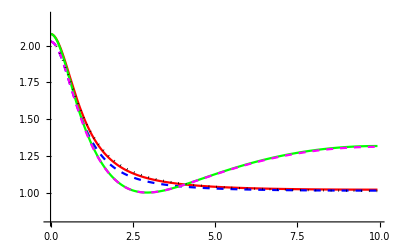

```mathematica
(* implicit schemes *)
alphaVal=0.5;betaVal=5.;
Plot[{SkImMidTau[xi]/.{a->alphaVal,b->betaVal,C->CVal},SkImMidSSA[xi]/.{a->alphaVal,b->betaVal,C->CVal},SkCN2Tau2ndCN2[xi]/.{a->alphaVal,b->betaVal,C->CVal},SkCN2SSACN2[xi]/.{a->alphaVal,b->betaVal,C->CVal},Sk0[xi]/.C->CVal},{xi,0,Sqrt[betaVal/alphaVal]Pi},PlotStyle->{Red,{Blue,Dashed},Green,{Magenta,Dashed},{Black,Dotted}},PlotRange->{0.8,2.2}]
```

## Further Analysis

```mathematica
CVal=2;
S1[xi_,alpha_,beta_]:=Evaluate[SkExMidTau[xi]/.{a->alpha,b->beta,C->CVal}]
S2[xi_,alpha_,beta_]:=Evaluate[SkExMidSSA[xi]/.{a->alpha,b->beta,C->CVal}]
Sexact[xi_]:=Evaluate[Sk0[xi]/.C->CVal]
```

```mathematica
Manipulate[Plot[{S1[xi,alpha,beta],S2[xi,alpha,beta],Sexact[xi]},{xi,0,Pi Sqrt[beta/alpha]},PlotStyle->{Red,{Blue,Dashed},{Black,Dotted}},PlotRange->{0.8,2.2}],{alpha,0.01,0.1},{beta,0.1,0.5}]
```

```mathematica
Manipulate[Plot[Boole[(S1[xi,alpha,beta]-Sexact[xi])^2<(S2[xi,alpha,beta]-Sexact[xi])^2],{xi,0,Pi Sqrt[beta/alpha]},PlotStyle->Red,PlotRange->{-0.1,1.1}],{alpha,0.01,0.1},{beta,0.1,0.5}]
```